## Model

### Variables

```mathematica
(*B0 to be determined with regression.*)
R =  0.02; (*Tube radius (m).*)
z0 = 0.035; (*Drop height from solenoid (m).*)
g = 9.8; (*Gravitational acceleration (m/s^2)*)
NT = 10; (*Number of wire turns.*)
Clear[B0]
```

### Models

```mathematica
AccelMotion[t_] := z0 - g t^2/2;
Field[z_] := NT B0 R^3/(R^2+z^2)^(3/2);

AccelField[t_] := Composition[Field, AccelMotion][t]
AccelVoltage[t_] := -Pi R^2 AccelField'[t]
```

### Minima

```mathematica
Clear[B0]
(*Finding minimum after time t = 0 of AccelFlux.*)
minimumVoltageModel = t/.Solve[AccelVoltage'[t] == 0, t, Reals][[3]];
(*Shifting AccelFlux minimum to t = 0.*)
AccelVoltageShifted[t_] := AccelVoltage[t + minimumVoltageModel];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

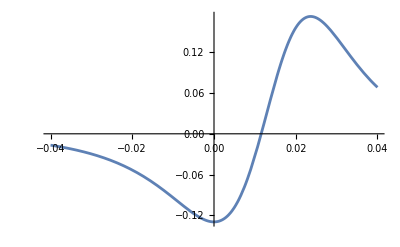

```mathematica
Clear[B0]
B0 = 0.34;
Plot[AccelVoltage[t], {t, 0, 1}];
Plot[AccelVoltageShifted[t], {t, -0.04, 0.04}, PlotRange->All]
```

```mathematica
100000
```

100000

## Data

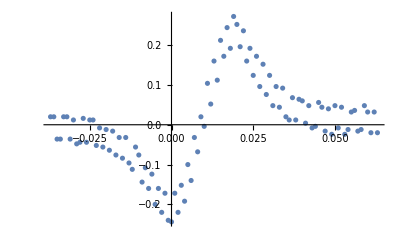

```mathematica
notePath = NotebookDirectory[];
fileName = "inputData\\old\\data_test_cleaned.txt";
fullName = StringJoin[{notePath, "\\", fileName}];
data = Import[fullName, "Data"];
data = data[[300;;400]];

(*We'll shift the data so as to have the first minimum at t = 0.*)
positionOfMinimum = Position[data[[All, 2]], Min[data[[All, 2]]]][[1, 1]];
timeOfMinimum = data[[positionOfMinimum, 1]];

data = MapAt[# - timeOfMinimum &, data, {All, 1}];
dataPlot = ListPlot[data]
```

## Fitting

NonlinearModelFit::nrlnum: The function value {-0.02+AccelVoltageShifted[-0.037],-0.02+AccelVoltageShifted[-0.0360003],0.036+AccelVoltageShifted[-0.035],0.036+AccelVoltageShifted[-0.034],-0.02+AccelVoltageShifted[-«21»],«1»,0.036+«1»,-0.012+AccelVoltageShifted[-0.03],0.048+AccelVoltageShifted[-0.029],0.044+AccelVoltageShifted[-0.028],«91»} is not a list of real numbers with dimensions {101} at {B0} = {1.}.

General::ivar: -0.0999959 is not a valid variable.

General::ivar: -0.0959143 is not a valid variable.

General::ivar: -0.0918326 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {-0.02+AccelVoltageShifted[-0.037],-0.02+AccelVoltageShifted[-0.0360003],0.036+AccelVoltageShifted[-0.035],0.036+AccelVoltageShifted[-0.034],-0.02+AccelVoltageShifted[-«21»],«1»,0.036+«1»,-0.012+AccelVoltageShifted[-0.03],0.048+AccelVoltageShifted[-0.029],0.044+AccelVoltageShifted[-0.028],«91»} is not a list of real numbers with dimensions {101} at {B0} = {1.}.

ReplaceAll::reps: {NonlinearModelFit[{{-0.037,0.02},{-0.0360003,0.02},{-0.035,-0.036},{-0.034,-0.036},{-0.033,0.02},{-0.032,0.02},{-0.031,-0.036},{-0.03,0.012},{-0.029,-0.048},{-0.028,-0.044},«91»},AccelVoltageShifted[t],B0,t][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NonlinearModelFit::nrlnum: The function value {-0.02+AccelVoltageShifted[-0.037],-0.02+AccelVoltageShifted[-0.0360003],0.036+AccelVoltageShifted[-0.035],0.036+AccelVoltageShifted[-0.034],-0.02+AccelVoltageShifted[-«21»],«1»,0.036+«1»,-0.012+AccelVoltageShifted[-0.03],0.048+AccelVoltageShifted[-0.029],0.044+AccelVoltageShifted[-0.028],«91»} is not a list of real numbers with dimensions {101} at {B0} = {1.}.

ReplaceAll::reps: {NonlinearModelFit[{{-0.037,0.02},{-0.0360003,0.02},{-0.035,-0.036},{-0.034,-0.036},{-0.033,0.02},{-0.032,0.02},{-0.031,-0.036},{-0.03,0.012},{-0.029,-0.048},{-0.028,-0.044},«91»},AccelVoltageShifted[t],B0,t][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

B0/.NonlinearModelFit[{{-0.037,0.02},{-0.0360003,0.02},{-0.035,-0.036},{-0.034,-0.036},{-0.033,0.02},{-0.032,0.02},{-0.031,-0.036},{-0.03,0.012},{-0.029,-0.048},{-0.028,-0.044},{-0.027,0.016},{-0.026,-0.044},{-0.025,0.012},{-0.024,0.012},{-0.023,-0.052},{-0.022,-0.008},{-0.021,-0.056},{-0.02,-0.012},{-0.019,-0.064},{-0.018,-0.016},{-0.017,-0.076},{-0.016,-0.032},{-0.015,-0.084},{-0.014,-0.032},{-0.013,-0.096},{-0.012,-0.112},{-0.011,-0.056},{-0.01,-0.076},{-0.009,-0.144},{-0.008,-0.108},{-0.007,-0.16},{-0.006,-0.124},{-0.005,-0.2},{-0.004,-0.16},{-0.003,-0.22},{-0.002,-0.172},{-0.001,-0.24},{0.,-0.244},{0.001,-0.172},{0.002,-0.22},{0.003,-0.152},{0.004,-0.192},{0.005,-0.1},{0.006,-0.14},{0.007,-0.032},{0.008,-0.068},{0.009,0.02},{0.01,-0.004},{0.011,0.104},{0.012,0.052},{0.013,0.16},{0.014,0.112},{0.015,0.212},{0.016,0.172},{0.017,0.244},{0.018,0.192},{0.019,0.272},{0.02,0.252},{0.021,0.196},{0.022,0.236},{0.023,0.16},{0.024,0.192},{0.025,0.124},{0.026,0.172},{0.027,0.096},{0.028,0.152},{0.029,0.076},{0.03,0.124},{0.031,0.048},{0.032,0.096},{0.033,0.044},{0.034,0.092},{0.035,0.02},{0.036,0.012},{0.037,0.068},{0.038,0.012},{0.039,0.064},{0.04,0.06},{0.041,0.004},{0.042,0.048},{0.043,-0.008},{0.044,-0.004},{0.045,0.056},{0.046,0.044},{0.047,-0.016},{0.048,0.04},{0.049,-0.024},{0.05,0.048},{0.051,-0.008},{0.052,0.044},{0.053,-0.024},{0.054,-0.012},{0.055,0.032},{0.056,0.036},{0.057,-0.016},{0.058,-0.012},{0.059,0.048},{0.06,0.032},{0.061,-0.02},{0.062,0.032},{0.063,-0.02}},AccelVoltageShifted[t],B0,t][BestFitParameters]

NonlinearModelFit::nrlnum: The function value {-0.02+AccelVoltageShifted[-0.037],-0.02+AccelVoltageShifted[-0.0360003],0.036+AccelVoltageShifted[-0.035],0.036+AccelVoltageShifted[-0.034],-0.02+AccelVoltageShifted[-«21»],«1»,0.036+«1»,-0.012+AccelVoltageShifted[-0.03],0.048+AccelVoltageShifted[-0.029],0.044+AccelVoltageShifted[-0.028],«91»} is not a list of real numbers with dimensions {101} at {B0} = {1.}.

NonlinearModelFit[{{-0.037,0.02},{-0.0360003,0.02},{-0.035,-0.036},{-0.034,-0.036},{-0.033,0.02},{-0.032,0.02},{-0.031,-0.036},{-0.03,0.012},{-0.029,-0.048},{-0.028,-0.044},{-0.027,0.016},{-0.026,-0.044},{-0.025,0.012},{-0.024,0.012},{-0.023,-0.052},{-0.022,-0.008},{-0.021,-0.056},{-0.02,-0.012},{-0.019,-0.064},{-0.018,-0.016},{-0.017,-0.076},{-0.016,-0.032},{-0.015,-0.084},{-0.014,-0.032},{-0.013,-0.096},{-0.012,-0.112},{-0.011,-0.056},{-0.01,-0.076},{-0.009,-0.144},{-0.008,-0.108},{-0.007,-0.16},{-0.006,-0.124},{-0.005,-0.2},{-0.004,-0.16},{-0.003,-0.22},{-0.002,-0.172},{-0.001,-0.24},{0.,-0.244},{0.001,-0.172},{0.002,-0.22},{0.003,-0.152},{0.004,-0.192},{0.005,-0.1},{0.006,-0.14},{0.007,-0.032},{0.008,-0.068},{0.009,0.02},{0.01,-0.004},{0.011,0.104},{0.012,0.052},{0.013,0.16},{0.014,0.112},{0.015,0.212},{0.016,0.172},{0.017,0.244},{0.018,0.192},{0.019,0.272},{0.02,0.252},{0.021,0.196},{0.022,0.236},{0.023,0.16},{0.024,0.192},{0.025,0.124},{0.026,0.172},{0.027,0.096},{0.028,0.152},{0.029,0.076},{0.03,0.124},{0.031,0.048},{0.032,0.096},{0.033,0.044},{0.034,0.092},{0.035,0.02},{0.036,0.012},{0.037,0.068},{0.038,0.012},{0.039,0.064},{0.04,0.06},{0.041,0.004},{0.042,0.048},{0.043,-0.008},{0.044,-0.004},{0.045,0.056},{0.046,0.044},{0.047,-0.016},{0.048,0.04},{0.049,-0.024},{0.05,0.048},{0.051,-0.008},{0.052,0.044},{0.053,-0.024},{0.054,-0.012},{0.055,0.032},{0.056,0.036},{0.057,-0.016},{0.058,-0.012},{0.059,0.048},{0.06,0.032},{0.061,-0.02},{0.062,0.032},{0.063,-0.02}},AccelVoltageShifted[t],B0,t][ParameterTable]

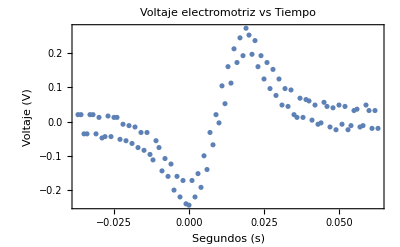

```mathematica
Clear[B0]
fitModel = NonlinearModelFit[data, AccelVoltageShifted[t], B0, t];fitPlot = Plot[fitModel[t], {t, -0.1, 0.1}, PlotStyle->Red, PlotRange->All];

accelPlot = Plot[AccelVoltageShifted[t], {t,-0.05, 0.06}, PlotStyle->Green , PlotRange->All];

B0Fitted = B0/.fitModel["BestFitParameters"]
parameterTable = fitModel["ParameterTable"]

Show[fitPlot, dataPlot, accelPlot, PlotLabel->"Voltaje electromotriz vs Tiempo", Frame->True, FrameLabel->{"Segundos (s)", "Voltaje (V)"}]
```